# Domača naloga 1

## 1. Naloga : Geometrija

V: Gasilci imajo 260 dm dolgo lestev. Kako visoko na stolpnico jo lahko prislonijo, če morajo
zaradi napačno parkiranih avtomobilov lestev postaviti 1000 cm od stolpnice?

```mathematica
lestev = UnitConvert[Quantity[260,"Decimeters"],"Meters"]; razmak = UnitConvert[Quantity[1000,"Centimeters"],"Meters"];
višina = √(lestev^2 - razmak^2)
```

24 m

O : Lestev lahko prislonijo na 24 m visoko stolpnico.

## 2. Naloga : Kotne funkcije v pravokotnem trikotniku

Spremeni zapis kota iz decimalnega v stopinje in minute ali obratno :

a)

```mathematica
DMSList[75.26]
```

{75,15,36.}

```mathematica
DMSString[{75,15,36.00000000001842}]
```

75°15'36.000"

b)

```mathematica
DMSList[48.679]
```

{48,40,44.4}

```mathematica
DMSString[{48,40,44.40000000000737}]
```

48°40'44.400"

c)

```mathematica
Quantity[FromDMS["52°36'"],"Degrees"] //N
```

52.6 °

d)

```mathematica
DMSList[19.5147]
```

{19,30,52.92}

```mathematica
DMSString[{19,30,52.92000000000456}]
```

19°30'52.920"

e)

```mathematica
Quantity[FromDMS["34°28'"],"Degrees"] //N
```

34.4667 °

f)

```mathematica
Quantity[FromDMS["8°57'"],"Degrees"] //N
```

8.95 °

## 3. Naloga : Računanje s koreni

Delno koreni :

a)

```mathematica
√18
```

3 √2

b)

```mathematica
√20
```

2 √5

c)

```mathematica
√27
```

3 √3

d)

```mathematica
√40
```

2 √10

e)

```mathematica
√45
```

3 √5

f)

```mathematica
√48
```

4 √3

g)

```mathematica
√54
```

3 √6

h)

```mathematica
√98
```

7 √2

i)

```mathematica
√117
```

3 √13

j)

```mathematica
√125
```

5 √5

k)

```mathematica
√126
```

3 √14

l)

```mathematica
√128
```

8 √2

m)

```mathematica
√180
```

6 √5

n)

```mathematica
√150
```

5 √6

o)

```mathematica
√450
```

15 √2

## 4. Naloga : Potence z racionalnim eksponentom

a)

```mathematica
25^(3/2)--8^(1/3)+(0.2)^-1
```

129.-1.73205 ⅈ

b)

```mathematica
2187^(5/7)*(5(-4)-9^-2)
```

-4863

c)

```mathematica
8^(4/3)*(-1)^6+(35-81^(1/4))^(1/5)
```

18

d)

```mathematica
DecimalForm[16^(3/4)*(0.1)^-1-243^(2/5)+(1/2)^-3]
```

79.

e)

```mathematica
DecimalForm[(125^2)^(1/3)*(0.1)^-1-(29+√9)^(1/5)]
```

248.

f)

```mathematica
64^(5/6)*(-1)^9-(-5)^3*(8^0-25^(-1/2) )
```

68

## 5. Naloga : Kvadratna funkcija

Graf kvadratne funkcije f(x) = a * x^2 gre skozi točko A(-2,6) . Poišči njeno enačbo.

```mathematica
ClearAll[x,y,a]
y:=a * x^2;
x = -2; 
Solve[y==6,a]
```

{{a→3/2}}

## 6. Naloga : Ploščine geometrijskih likov

Izračunaj ploščino trikotnika in polmera trikotniku včrtanega ter očrtanega kroga, če stranice merijo:

a) a = 13cm, b = 11cm, c = 20cm

```mathematica
ClearAll[a,b,c]
a =13;
b = 11;
c = 20;
s = (a+b+c)/2;
S = s*(s-a)(s-b)(s-c)
```

b) a = 31/4dm, b = 5dm, c = 51/4dm

c) a = 14m, b = 10m, c = 6m

## 7. Naloga : Polinomi – 1

Izračunaj produkt polinomov p(x) = 2 x^4 - 3 x^3 + 5x - 2 in q(x) = 5 x^3 + 2 x^2 - 3

```mathematica
ClearAll[p,q]
p = 2 x^4-3 x^3+5x-2 ;
q = 5 x^3+2 x^2-3;
produkt = p * q;
Collect[produkt,x]
```

6-15 x-4 x^2+9 x^3+19 x^4-6 x^5-11 x^6+10 x^7

## 8. Naloga :– Polinomi – 2

Določi neznani koeficient tako, da bo imel polinom zahtevano ničlo:

a) p(x) = x^3 - 2 x^2 -18x + (a + 50), x = 4

```mathematica
ClearAll[p,x]
p=x^3-2 x^2-18x+(a+50);
x = 4;
CoefficientList[p,a]
```

{10,1}

b) p(x) = x^3 + (a + 3)x^2 - 11x -10, x = -2

```mathematica
ClearAll[p,x]
p=x^3+(a+3)x^2-11x-10;
x = -2;
CoefficientList[p,a]
```

{16,4}

## 9. Naloga : Racionalna funkcija – 1

Izračunaj ničle racionalne funkcije:

a) f(x) = (x^2- 2x - 8)/(x^2 - 6x + 5)

```mathematica
ClearAll[x,f]
f=(x^2- 2x - 8)/(x^2 - 6x + 5);
Solve[f==0,x]
```

{{x→-2},{x→4}}

b) f(x) = (x^2+ 8x + 16)/(-x + 6)

```mathematica
ClearAll[x,f]
f=(x^2+ 8x + 16)/(-x + 6);
Solve[f==0,x]
```

{{x→-4},{x→-4}}

c) f(x) = (12 x^3+ 8 x^2 -3x - 2)/(2 x^2+ 4x + 8)

```mathematica
ClearAll[x,f]
f=(12 x^3+ 8 x^2 -3x - 2)/(2 x^2+ 4x + 8);
Solve[f==0,x]
```

{{x→-2/3},{x→-1/2},{x→1/2}}

## 10. Naloga : Racionalna funkcija – 2

Nariši graf racionalne funkcije:

a) f(x) = (x^2- 4x + 3)/(x - 2)

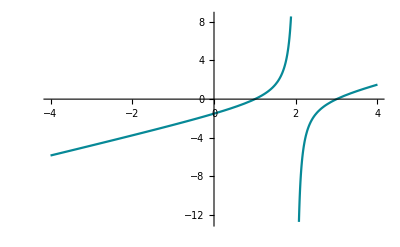

```mathematica
ClearAll[x,f]
f=(x^2- 4x + 3)/(x - 2);
Plot[f,{x,-4,4}]
```

b) f(x) = (x^2- x - 2)/(-x + 3)

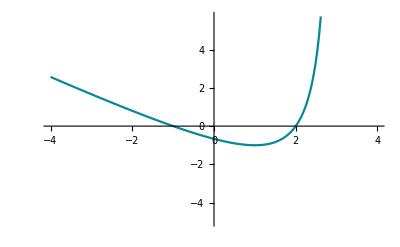

```mathematica
ClearAll[x,f]
f=(x^2- x - 2)/(-x + 3);
Plot[f,{x,-4,4}]
```

c) f(x) = (x^2+ 4x + 4)/(x + 1)

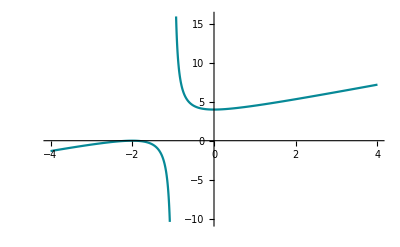

```mathematica
ClearAll[x,f]
f=(x^2+ 4x + 4)/(x + 1);
Plot[f,{x,-4,4}]
```

d) f(x) = (x^2+ x)/(x + 2)

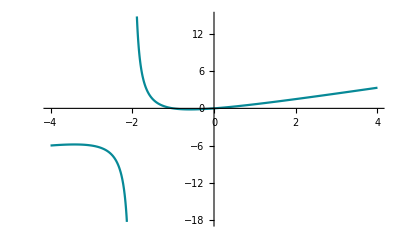

```mathematica
ClearAll[x,f]
f=(x^2+ x)/(x + 2);
Plot[f,{x,-4,4}]
```